# Thesis Figures

## Run Catalogue

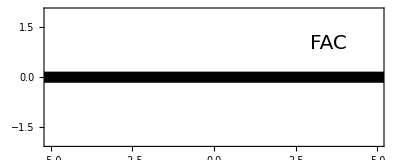

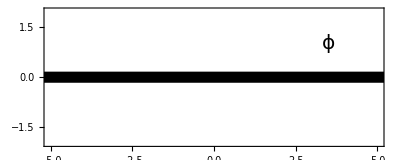

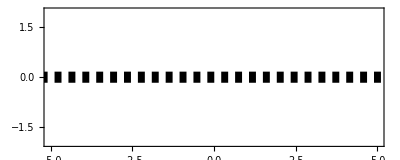

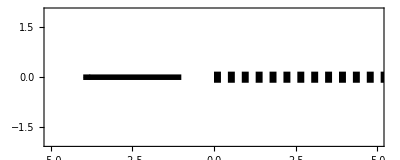

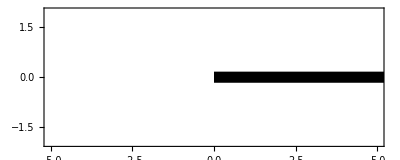

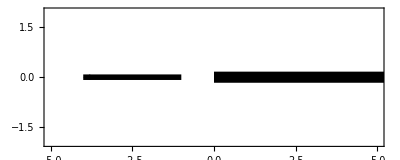

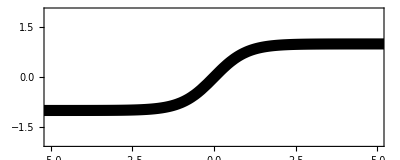

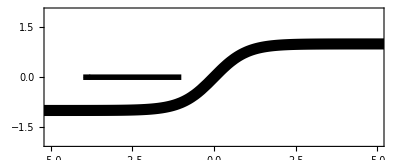

```mathematica
baseJ=Plot[0,{x,-10,10},PlotRange->{{-5,5},{-2,2}},PlotStyle->{Thickness[0.02],Black},Frame->True,Axes->None,FrameTicks->None,AspectRatio->2/5,
Prolog->{Text[Style["FAC",20],{3.5,1}]}]
baseF=Plot[0,{x,-10,10},PlotRange->{{-5,5},{-2,2}},PlotStyle->{Thickness[0.02],Black},Frame->True,Axes->None,FrameTicks->None,AspectRatio->2/5,
Prolog->{Text[Style["ϕ",20],{3.5,1}]}]
deep=Plot[0,{x,-10,10},PlotRange->{{-5,5},{-2,2}},PlotStyle->{Thickness[0.02],Black,Dashed},Frame->True,Axes->None,FrameTicks->None,AspectRatio->2/5]
deepm=Plot[0,{x,0,10},PlotRange->{{-5,5},{-2,2}},PlotStyle->{Thickness[0.02],Black,Dashed},Frame->True,Axes->None,FrameTicks->None,AspectRatio->2/5,Prolog->{Arrowheads[0.1],Thickness[0.01],Arrow[{{-1,0},{-4,0}}]}]
sharc=Plot[0,{x,0,10},PlotRange->{{-5,5},{-2,2}},PlotStyle->{Thickness[0.02],Black},Frame->True,Axes->None,FrameTicks->None,AspectRatio->2/5]
sharcm=Plot[0,{x,0,10},PlotRange->{{-5,5},{-2,2}},PlotStyle->{Thickness[0.02],Black},Frame->True,Axes->None,FrameTicks->None,AspectRatio->2/5,Prolog->{Arrowheads[0.1],Thickness[0.01],Arrow[{{-1,0},{-4,0}}]}]
bend=Plot[Tanh[x],{x,-10,10},PlotRange->{{-5,5},{-2,2}},PlotStyle->{Thickness[0.02],Black},Frame->True,Axes->None,FrameTicks->None,AspectRatio->2/5]
bendm=Plot[Tanh[x],{x,-10,10},PlotRange->{{-5,5},{-2,2}},PlotStyle->{Thickness[0.02],Black},Frame->True,Axes->None,FrameTicks->None,AspectRatio->2/5,Prolog->{Arrowheads[0.1],Thickness[0.01],Arrow[{{-1,0},{-4,0}}]}]
timed=Plot[0,{x,-10,10},PlotRange->{{-5,5},{-2,2}},PlotStyle->{Thickness[0.02],Black},Frame->True,Axes->None,FrameTicks->None,AspectRatio->2/5,Prolog->{Text[Style["Δt",20],{3.5,1}]}]
bendbar=Plot[Tanh[x],{x,-2,10},PlotRange->{{-5,5},{-2,2}},PlotStyle->{Thickness[0.02],Black},Frame->True,Axes->None,FrameTicks->None,AspectRatio->2/5,Prolog->{Arrowheads[0.1],Thickness[0.01],Arrow[{{-2.5,-1},{-4,-1}}]}]
catalog=GraphicsGrid[{
{
Graphics[{White,Circle[]}]
,deep
,deepm
}
,{
baseJ
,bend
,bendm
}
,{
baseF
,timed
,bendbar
}
,{
Graphics[{White,Circle[]}]
,sharc
,sharcm
}
},Spacings->{200,30}]
```

```mathematica
Export[NotebookDirectory[]<>"catalog_tmp.png",catalog]
```

D:\Files\Research\Thesis\Proposal\catalog_tmp.png

## Data Slice Example

```mathematica
Import["D:\\Files\\Research\\Thesis\\Proposal\\SW_EXPT_EFIC_TIICT_20140422_0844T0849_fsmi.h5"]//TableForm
```

/event/Altitude_km
/event/Brightness_Vector
/event/By
/event/Clouds
/event/Date_Time_in_UT
/event/FAC_micro
/event/Flow
/event/Footpoint_Lat
/event/Footpoint_Long
/event/Framechoice
/event/Geodetic_Latitude_deg
/event/Image_Flag
/event/Image_Timestamp
/event/Images
/event/Longitude_deg
/event/Magnetic_Local_Time
/event/PathX
/event/PathY
/event/QD_Magnetic_Lat
/event/Quality
/event/Satellite
/event/Satellite_Velocity_N
/event/Skymap/BIN_AZIMUTH
/event/Skymap/BIN_COLUMN
/event/Skymap/BIN_ELEVATION
/event/Skymap/BIN_MAP_ALTITUDE
/event/Skymap/BIN_MAP_LATITUDE
/event/Skymap/BIN_MAP_LONGITUDE
/event/Skymap/BIN_ROW
/event/Skymap/FULL_AZIMUTH
/event/Skymap/FULL_BIN
/event/Skymap/FULL_COLUMN
/event/Skymap/FULL_ELEVATION
/event/Skymap/FULL_IGNORE
/event/Skymap/FULL_MAP_ALTITUDE
/event/Skymap/FULL_MAP_LATITUDE
/event/Skymap/FULL_MAP_LONGITUDE
/event/Skymap/FULL_MULTIPLY
/event/Skymap/FULL_ROW
/event/Skymap/FULL_SUBTRACT
/event/Skymap/GENERATION_INFO/AUTHOR
/event/Skymap/GENERATION_INFO/BYTSCL_VALUES
/event/Skymap/GENERATION_INFO/CCD_CENTER
/event/Skymap/GENERATION_INFO/CODE_USED
/event/Skymap/GENERATION_INFO/DATA_LOC
/event/Skymap/GENERATION_INFO/DATE_GENERATED
/event/Skymap/GENERATION_INFO/DATE_TIME_USED
/event/Skymap/GENERATION_INFO/IMG_FLIP
/event/Skymap/GENERATION_INFO/OPTICAL_ORIENTATION
/event/Skymap/GENERATION_INFO/OPTICAL_PROJECTION
/event/Skymap/GENERATION_INFO/PIXEL_ASPECT_RATIO
/event/Skymap/GENERATION_INFO/VALID_INTERVAL_START
/event/Skymap/GENERATION_INFO/VALID_INTERVAL_STOP
/event/Skymap/IMAGER_UID
/event/Skymap/IMAGER_UNIX_TIME
/event/Skymap/PROJECT_UID
/event/Skymap/SITE_MAP_ALTITUDE
/event/Skymap/SITE_MAP_LATITUDE
/event/Skymap/SITE_MAP_LONGITUDE
/event/Skymap/SITE_UID
/event/Smooth_Brightness
/event/UT
/event/Unofficial_crosstrack_flow

```mathematica
Import["D:\\Files\\Research\\Thesis\\Proposal\\SW_EXPT_EFIC_TIICT_20140422_0844T0849_fsmi.h5","/event/Geodetic_Latitude_deg"]
Import["D:\\Files\\Research\\Thesis\\Proposal\\SW_EXPT_EFIC_TIICT_20140422_0844T0849_fsmi.h5","/event/Longitude_deg"]
```

{{52.7395,52.7714,52.8033,52.8352,52.8671,52.899,52.9309,52.9628,52.9947,53.0266,53.0585,53.0904,53.1223,53.1542,53.186,53.2179,53.2498,53.2817,53.3136,53.3455,53.3774,53.4093,53.4412,53.4731,53.505,53.5369,53.5688,53.6007,53.6326,53.6645,53.6964,53.7283,53.7601,53.792,53.8239,53.8558,53.8877,53.9196,53.9515,53.9834,54.0153,54.0472,54.0791,54.111,54.1429,54.1747,54.2066,54.2385,54.2704,54.3023,54.3342,54.3661,54.398,54.4299,54.4618,54.4937,54.5256,54.5574,54.5893,54.6212,54.6531,54.685,54.7169,54.7488,54.7807,54.8126,54.8444,54.8763,54.9082,54.9401,54.972,55.0039,55.0358,55.0677,55.0996,55.1314,55.1633,55.1952,55.2271,55.259,55.2909,55.3228,55.3546,55.3865,55.4184,55.4503,55.4822,55.5141,55.546,55.5779,55.6097,55.6416,55.6735,55.7054,55.7373,55.7692,55.801,55.8329,55.8648,55.8967,55.9286,55.9605,55.9923,56.0242,56.0561,56.088,56.1199,56.1518,56.1837,56.2155,56.2474,56.2793,56.3112,56.3431,56.3749,56.4068,56.4387,56.4706,56.5025,56.5343,56.5662,56.5981,56.63,56.6619,56.6937,56.7256,56.7575,56.7894,56.8213,56.8531,56.885,56.9169,56.9488,56.9807,57.0125,57.0444,57.0763,57.1082,57.14,57.1719,57.2038,57.2357,57.2676,57.2994,57.3313,57.3632,57.3951,57.4269,57.4588,57.4907,57.5226,57.5544,57.5863,57.6182,57.6501,57.6819,57.7138,57.7457,57.7776,57.8094,57.8413,57.8732,57.9051,57.9369,57.9688,58.0007,58.0325,58.0644,58.0963,58.1282,58.16,58.1919,58.2238,58.2556,58.2875,58.3194,58.3513,58.3831,58.415,58.4469,58.4787,58.5106,58.5425,58.5743,58.6062,58.6381,58.6699,58.7018,58.7337,58.7655,58.7974,58.8293,58.8611,58.893,58.9249,58.9567,58.9886,59.0205,59.0523,59.0842,59.1161,59.1479,59.1798,59.2117,59.2435,59.2754,59.3073,59.3391,59.371,59.4028,59.4347,59.4666,59.4984,59.5303,59.5622,59.594,59.6259,59.6577,59.6896,59.7215,59.7533,59.7852,59.817,59.8489,59.8808,59.9126,59.9445,59.9763,60.0082,60.0401,60.0719,60.1038,60.1356,60.1675,60.1994,60.2312,60.2631,60.2949,60.3268,60.3586,60.3905,60.4223,60.4542,60.4861,60.5179,60.5498,60.5816,60.6135,60.6453,60.6772,60.709,60.7409,60.7727,60.8046,60.8364,60.8683,60.9001,60.932,60.9638,60.9957,61.0275,61.0594,61.0912,61.1231,61.1549,61.1868,61.2186,61.2505,61.2823,61.3142,61.346,61.3779,61.4097,61.4416,61.4734,61.5053,61.5371,61.569,61.6008,61.6326,61.6645,61.6963,61.7282,61.76,61.7919,61.8237,61.8556,61.8874,61.9192,61.9511,61.9829,62.0148,62.0466,62.0784,62.1103,62.1421,62.174,62.2058,62.2376,62.2695,62.3013,62.3332,62.365,62.3968,62.4287,62.4605,62.4923,62.5242,62.556,62.5879,62.6197,62.6515,62.6833,62.7152,62.747,62.7789,62.8107,62.8425,62.8744,62.9062,62.938,62.9698,63.0017,63.0335,63.0653,63.0972,63.129,63.1608,63.1927,63.2245,63.2563,63.2881,63.32,63.3518,63.3836,63.4155,63.4473,63.4791,63.5109,63.5428,63.5746,63.6064,63.6382,63.6701,63.7019,63.7337,63.7655,63.7973,63.8292,63.861,63.8928,63.9246,63.9565,63.9883,64.0201,64.0519,64.0837,64.1155,64.1474,64.1792,64.211,64.2428,64.2746,64.3064,64.3383,64.3701,64.4019,64.4337,64.4655,64.4973,64.5291,64.561,64.5928,64.6246,64.6564,64.6882,64.72,64.7518,64.7836,64.8154,64.8473,64.8791,64.9109,64.9427,64.9745,65.0063,65.0381,65.0699,65.1017,65.1335,65.1653,65.1971,65.2289,65.2607,65.2925,65.3243,65.3561,65.3879,65.4197,65.4515,65.4833,65.5151,65.5469,65.5787,65.6105,65.6423,65.6741,65.7059,65.7377,65.7695,65.8013,65.8331,65.8649,65.8967,65.9285,65.9603,65.9921,66.0239,66.0556,66.0874,66.1192,66.151,66.1828,66.2146,66.2464,66.2782,66.31,66.3417,66.3735,66.4053,66.4371,66.4689,66.5007,66.5324,66.5642,66.596,66.6278,66.6596,66.6914,66.7231,66.7549,66.7867,66.8185,66.8502,66.882,66.9138,66.9456,66.9774,67.0091,67.0409,67.0727,67.1045,67.1362,67.168,67.1998,67.2315,67.2633,67.2951,67.3269,67.3586,67.3904,67.4222,67.4539,67.4857,67.5174,67.5492,67.581,67.6127,67.6445,67.6763,67.708,67.7398,67.7715,67.8033,67.8351,67.8668,67.8986,67.9303,67.9621,67.9939,68.0256,68.0574,68.0891,68.1209,68.1526,68.1844,68.2161,68.2479,68.2796,68.3114,68.3431,68.3749,68.4066,68.4384,68.4701,68.5019,68.5336,68.5653,68.5971,68.6288,68.6606,68.6923,68.7241,68.7558,68.7875,68.8193,68.851,68.8827,68.9145,68.9462,68.9779,69.0097,69.0414,69.0731,69.1049,69.1366,69.1683,69.2001,69.2318,69.2635,69.2952,69.327,69.3587,69.3904,69.4221,69.4539,69.4856,69.5173,69.549,69.5807,69.6125,69.6442,69.6759,69.7076,69.7393,69.771,69.8027,69.8345,69.8662,69.8979,69.9296,69.9613,69.993,70.0247,70.0564,70.0881,70.1198,70.1515,70.1832,70.2149,70.2466,70.2783,70.31,70.3417,70.3734,70.4051,70.4368,70.4685,70.5002,70.5319,70.5636,70.5953,70.627,70.6587,70.6904,70.722,70.7537,70.7854,70.8171,70.8488,70.8805,70.9121,70.9438,70.9755,71.0072,71.0388,71.0705,71.1022,71.1339,71.1655,71.1972,71.2289,71.2606,71.2922,71.3239,71.3556,71.3872,71.4189,71.4505,71.4822,71.5139,71.5455,71.5772,71.6088,71.6405,71.6721,71.7038,71.7355,71.7671,71.7988}}

{{-108.833,-108.831,-108.829,-108.827,-108.825,-108.823,-108.821,-108.819,-108.817,-108.815,-108.813,-108.811,-108.809,-108.807,-108.805,-108.803,-108.801,-108.799,-108.797,-108.795,-108.793,-108.791,-108.789,-108.787,-108.785,-108.783,-108.781,-108.779,-108.777,-108.774,-108.772,-108.77,-108.768,-108.766,-108.764,-108.762,-108.76,-108.757,-108.755,-108.753,-108.751,-108.749,-108.747,-108.744,-108.742,-108.74,-108.738,-108.736,-108.733,-108.731,-108.729,-108.727,-108.724,-108.722,-108.72,-108.718,-108.715,-108.713,-108.711,-108.709,-108.706,-108.704,-108.702,-108.699,-108.697,-108.695,-108.692,-108.69,-108.688,-108.685,-108.683,-108.68,-108.678,-108.676,-108.673,-108.671,-108.668,-108.666,-108.664,-108.661,-108.659,-108.656,-108.654,-108.651,-108.649,-108.646,-108.644,-108.641,-108.639,-108.636,-108.634,-108.631,-108.629,-108.626,-108.624,-108.621,-108.619,-108.616,-108.613,-108.611,-108.608,-108.606,-108.603,-108.6,-108.598,-108.595,-108.593,-108.59,-108.587,-108.585,-108.582,-108.579,-108.577,-108.574,-108.571,-108.568,-108.566,-108.563,-108.56,-108.558,-108.555,-108.552,-108.549,-108.546,-108.544,-108.541,-108.538,-108.535,-108.532,-108.53,-108.527,-108.524,-108.521,-108.518,-108.515,-108.512,-108.51,-108.507,-108.504,-108.501,-108.498,-108.495,-108.492,-108.489,-108.486,-108.483,-108.48,-108.477,-108.474,-108.471,-108.468,-108.465,-108.462,-108.459,-108.456,-108.453,-108.45,-108.447,-108.444,-108.441,-108.438,-108.435,-108.431,-108.428,-108.425,-108.422,-108.419,-108.416,-108.413,-108.409,-108.406,-108.403,-108.4,-108.397,-108.393,-108.39,-108.387,-108.384,-108.38,-108.377,-108.374,-108.37,-108.367,-108.364,-108.36,-108.357,-108.354,-108.35,-108.347,-108.344,-108.34,-108.337,-108.334,-108.33,-108.327,-108.323,-108.32,-108.316,-108.313,-108.309,-108.306,-108.302,-108.299,-108.295,-108.292,-108.288,-108.285,-108.281,-108.278,-108.274,-108.27,-108.267,-108.263,-108.26,-108.256,-108.252,-108.249,-108.245,-108.241,-108.238,-108.234,-108.23,-108.226,-108.223,-108.219,-108.215,-108.211,-108.208,-108.204,-108.2,-108.196,-108.192,-108.189,-108.185,-108.181,-108.177,-108.173,-108.169,-108.165,-108.161,-108.157,-108.154,-108.15,-108.146,-108.142,-108.138,-108.134,-108.13,-108.126,-108.122,-108.118,-108.113,-108.109,-108.105,-108.101,-108.097,-108.093,-108.089,-108.085,-108.08,-108.076,-108.072,-108.068,-108.064,-108.059,-108.055,-108.051,-108.047,-108.042,-108.038,-108.034,-108.03,-108.025,-108.021,-108.017,-108.012,-108.008,-108.003,-107.999,-107.995,-107.99,-107.986,-107.981,-107.977,-107.972,-107.968,-107.963,-107.959,-107.954,-107.95,-107.945,-107.94,-107.936,-107.931,-107.927,-107.922,-107.917,-107.913,-107.908,-107.903,-107.898,-107.894,-107.889,-107.884,-107.879,-107.875,-107.87,-107.865,-107.86,-107.855,-107.851,-107.846,-107.841,-107.836,-107.831,-107.826,-107.821,-107.816,-107.811,-107.806,-107.801,-107.796,-107.791,-107.786,-107.781,-107.776,-107.771,-107.766,-107.76,-107.755,-107.75,-107.745,-107.74,-107.735,-107.729,-107.724,-107.719,-107.714,-107.708,-107.703,-107.698,-107.692,-107.687,-107.681,-107.676,-107.671,-107.665,-107.66,-107.654,-107.649,-107.643,-107.638,-107.632,-107.627,-107.621,-107.616,-107.61,-107.604,-107.599,-107.593,-107.587,-107.582,-107.576,-107.57,-107.565,-107.559,-107.553,-107.547,-107.541,-107.536,-107.53,-107.524,-107.518,-107.512,-107.506,-107.5,-107.494,-107.488,-107.482,-107.476,-107.47,-107.464,-107.458,-107.452,-107.446,-107.44,-107.433,-107.427,-107.421,-107.415,-107.409,-107.402,-107.396,-107.39,-107.383,-107.377,-107.371,-107.364,-107.358,-107.351,-107.345,-107.339,-107.332,-107.326,-107.319,-107.312,-107.306,-107.299,-107.293,-107.286,-107.279,-107.273,-107.266,-107.259,-107.253,-107.246,-107.239,-107.232,-107.225,-107.218,-107.212,-107.205,-107.198,-107.191,-107.184,-107.177,-107.17,-107.163,-107.156,-107.149,-107.142,-107.134,-107.127,-107.12,-107.113,-107.106,-107.098,-107.091,-107.084,-107.077,-107.069,-107.062,-107.054,-107.047,-107.04,-107.032,-107.025,-107.017,-107.01,-107.002,-106.994,-106.987,-106.979,-106.971,-106.964,-106.956,-106.948,-106.94,-106.933,-106.925,-106.917,-106.909,-106.901,-106.893,-106.885,-106.877,-106.869,-106.861,-106.853,-106.845,-106.837,-106.829,-106.821,-106.812,-106.804,-106.796,-106.788,-106.779,-106.771,-106.763,-106.754,-106.746,-106.737,-106.729,-106.72,-106.712,-106.703,-106.695,-106.686,-106.677,-106.669,-106.66,-106.651,-106.642,-106.633,-106.625,-106.616,-106.607,-106.598,-106.589,-106.58,-106.571,-106.562,-106.553,-106.544,-106.534,-106.525,-106.516,-106.507,-106.497,-106.488,-106.479,-106.469,-106.46,-106.45,-106.441,-106.431,-106.422,-106.412,-106.403,-106.393,-106.383,-106.373,-106.364,-106.354,-106.344,-106.334,-106.324,-106.314,-106.304,-106.294,-106.284,-106.274,-106.264,-106.254,-106.244,-106.233,-106.223,-106.213,-106.203,-106.192,-106.182,-106.171,-106.161,-106.15,-106.14,-106.129,-106.118,-106.108,-106.097,-106.086,-106.075,-106.064,-106.054,-106.043,-106.032,-106.021,-106.01,-105.998,-105.987,-105.976,-105.965,-105.954,-105.942,-105.931,-105.92,-105.908,-105.897,-105.885,-105.874,-105.862,-105.85,-105.839,-105.827,-105.815,-105.803,-105.791,-105.78,-105.768,-105.756,-105.744,-105.731,-105.719,-105.707,-105.695,-105.683,-105.67,-105.658,-105.645,-105.633,-105.62,-105.608,-105.595,-105.583,-105.57,-105.557,-105.544,-105.531,-105.518,-105.505}}

```mathematica
Export[NotebookDirectory[]<>"placeholder.png",Graphics[{White,EdgeForm[Black],Rectangle[{0,0},{6,4}]}]]
```

D:\Files\Research\Thesis\placeholder.png

## Context

```mathematica
RE=6371000;
```

```mathematica
griddir="D:\\Files\\Research\\Thesis\\test_run\\simgrid.h5";
x1=Import[griddir,"/x1"][[3;;-3]];
x2=Import[griddir,"/x2"][[3;;-3]];
x3=Import[griddir,"/x3"][[3;;-3]];
x=Import[griddir,"/x"];
y=Import[griddir,"/y"];
z=Import[griddir,"/z"];
xyz=Transpose[{x,y,z},{4,1,2,3}];
model=ListPointPlot3D[{
Join[xyz[[;;,1,1]],xyz[[;;,-1,1]],xyz[[;;,1,-1]],xyz[[;;,-1,-1]]]
,Join[xyz[[1,;;,1]],xyz[[-1,;;,1]],xyz[[1,;;,-1]],xyz[[-1,;;,-1]]]
,Join[xyz[[1,1,;;]],xyz[[-1,1,;;]],xyz[[1,-1,;;]],xyz[[-1,-1,;;]]]
}
,ImageSize->Large
,BoxRatios->((-Subtract@@MinMax@Flatten[#])&/@{x,y,z})
,PlotStyle->Black
,Axes->False
,Boxed->False
];
```

```mathematica
sheet[y_,pos_,wdth_,gsl_]:=(Tanh[2(y-pos+wdth/2)/(gsl wdth)]-Tanh[2(y-pos-wdth/2)/(gsl wdth)])/2
contour[x_,span_,slope_]:=(span/2) Tanh[2slope x/span]
ctrSlope=1/2;
ctrSpan=100000;(*m*)
KAmp=0.3;(*A m^-1*)
JWdth=400000;(*m*)
JGSL=0.1;(*%*)
ctr[x_]:=contour[x,ctrSpan,ctrSlope]
J[x_,y_]:=(KAmp/JWdth) (sheet[y,ctr[x]+JWdth /2,JWdth,JGSL]-sheet[y,ctr[x]-JWdth /2,JWdth,JGSL])
j=Table[J[x,y],{y,x3},{x,x2}];
jdata=Flatten[Transpose[{x[[;;,;;,-1]],y[[;;,;;,-1]],z[[;;,;;,-1]],j},{3,1,2}],1];
jdatapos=Cases[jdata,{x_,y_,z_,f_}/;f>0.7 10^-6];
jdataneg=Cases[jdata,{x_,y_,z_,f_}/;f<-0.7 10^-6];
field=ListPointPlot3D[{jdatapos[[;;,;;3]],jdataneg[[;;,;;3]]},PlotStyle->{{Blue,PointSize[0.003]},{Red,PointSize[0.003]}},Axes->False,Boxed->False];
```

```mathematica
mag=Graphics3D[{Darker@Gray,BezierCurve[{xyz[[1,1,-1]],4xyz[[1,1,-1]],5RE{-0.5,-1,0}}],BezierCurve[{xyz[[1,-1,-1]],4xyz[[1,-1,-1]],5RE{0,-1,0}}],BezierCurve[{xyz[[-1,1,-1]],7xyz[[-1,1,-1]],5RE{-0.5,-1.1,0}}],BezierCurve[{xyz[[-1,-1,-1]],5xyz[[-1,-1,-1]],5RE{-0.2,-1.1,0}}]}];
magarrows=Graphics3D[{Arrowheads[0.003],Darker@Gray,,Arrow[{1.0001xyz[[1,1,-1]],xyz[[1,1,-1]]}],Arrow[{1.0001xyz[[1,-1,-1]],xyz[[1,-1,-1]]}],Arrow[{1.0001xyz[[-1,1,-1]],xyz[[-1,1,-1]]}],Arrow[{1.0001xyz[[-1,-1,-1]],xyz[[-1,-1,-1]]}]}];
```

```mathematica
off=RE{-0.05,0,0};
pot=Graphics3D[Table[{Darker@Green,BezierCurve[f{2.5xyz[[1/2 216,1,-1]]+off,RE{0,0,0},2.5xyz[[-1,1,-1]]+off}]},{f,1,1.18,0.06}]];
epar=Graphics3D[{Darker@Green,Arrowheads[0.005],Arrow[{1.2xyz[[3/4 216,1,-1]]+RE{0.03,0,0},1.6xyz[[3/4 216,1,-1]]+RE{0.03,0,0}}]}];
```

```mathematica
asiData=Import["D:\\Files\\Research\\ARCS\\example_aurora1.mat"];
asiFrame=24;
ArrayPlot[30000-Transpose@asiData[[3,asiFrame,6;;-40,50;;-80]],PlotRange->{0,30000}]
```

-Graphics-

```mathematica
earth=earthGraphic[11,RE];
```

```mathematica
context=Show[
earth
,model
,mag
,magarrows
,Graphics3D[Text[Style["B⃗",30,Darker@Gray],1.3xyz[[1,1,-1]],{4,0}]]
,pot
,epar
,field
,Graphics3D[Text[Style["(E⃗)_(||)",30,Darker@Green],1.4xyz[[3/4 216,1,1]],{0,0}]]
,Graphics3D[Text[Style["80 km",30],xyz[[1,1,1]],{1.2,1}]]
,Graphics3D[Text[Style["E ",30,Blue],xyz[[1,1,16]],{1.2,0}]]
,Graphics3D[{Blue,Sphere[xyz[[1,1,16]],50000]}]
,Graphics3D[Text[Style["F ",30,Blue],xyz[[1,1,111]],{1.2,0}]]
,Graphics3D[{Blue,Sphere[xyz[[1,1,111]],50000]}]
,Graphics3D[Text[Style["1000 km",30],xyz[[1,1,-1]],{1.2,0}]]
,Graphics3D[Text[Style["1-2 R_E",30],1.5xyz[[-1,1,-1]],{-1,0}]]
,Graphics3D[{Arrowheads[0.004],Thick,Arrow[{1.2xyz[[-1,-25,-1]],xyz[[-1,-20,-1]]}]}]
,Graphics3D[Text[Style["    GEMINI
Model Space",30],1.2xyz[[-1,-25,-1]],{0,-1}]]
,Graphics3D[{Arrowheads[0.004],Thick,Arrow[{1.3xyz[[-1,60,-1]],xyz[[-50,60,-1]]}]}]
,Graphics3D[Text[Style["2D Input Map",30],1.3xyz[[-1,60,-1]],{0,-1}]]
]
```

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"context_temp.png",context]
```

D:\Files\Research\Thesis\context_temp.png

```mathematica
Σ={{ΣP,-ΣH,0},{ΣH,ΣP,0},{0,0,0}};
Ep={E1,E2,E3};
delp={dx,dy,0};
s={0,0,1};
```

```mathematica
(Σ.Ep)
```

{-E2 ΣH+E1 ΣP,E1 ΣH+E2 ΣP,0}

```mathematica
Cross[Ep,s]
```

{E2,-E1,0}

```mathematica
-ΣH delp.(Cross[Ep,s])
```

-(-dy E1+dx E2) ΣH

```mathematica
Curl[Ep,{x,y,z}]
```

## 2-D versus 3D visualization

```mathematica
J1=Import["D:\\Files\\Research\\ARCS\\OSSE7_1b\\20150201_36000.000000.h5","/J1all"];
x1=Import["D:\\Files\\Research\\ARCS\\OSSE7_1b\\simgrid.h5","/x1"];
x3=Import["D:\\Files\\Research\\ARCS\\OSSE7_1b\\simgrid.h5","/x3"];
```

```mathematica
J1//Dimensions
```

{216,144,165}

```mathematica
x3[[3;;-3]]//Length
```

216

```mathematica
dat=Table[{x3[[2+x]],x1[[2+z]],J1[[x,70,z]]},{x,1,216},{z,1,165}];
```

```mathematica
dat//Dimensions
```

{216,165,3}

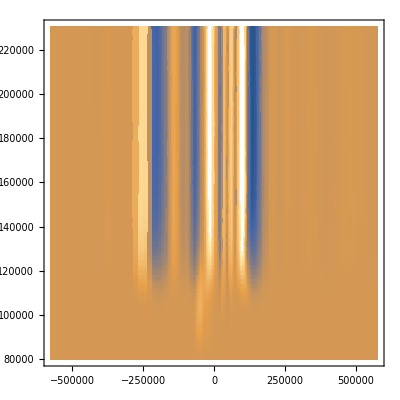

```mathematica
ListDensityPlot[Flatten[dat[[;;,;;70]],1],InterpolationOrder->0]
```

## GIF MAEVE DATA EXAMPLES

```mathematica
imgs=Table[Import["D:\\Files\\Research\\Thesis\\Proposal\\gif\\example_gemini_input"<>StringPadLeft[ToString[t],3,"0"]<>".png"],{t,1,300,10}];
Export[NotebookDirectory[]<>"example_gemini_input.gif",imgs, AnimationRepetitions->Infinity]
```

```mathematica
imgs=Table[Import["D:\\Files\\Research\\Thesis\\Proposal\\gif\\bent_moving"<>StringPadLeft[ToString[t],3,"0"]<>".png"],{t,10,300,10}];
Export[NotebookDirectory[]<>"bent_moving.gif",imgs, AnimationRepetitions->Infinity]
```

D:\Files\Research\Thesis\Proposal\bent_moving.gif

```mathematica
imgs=Table[Import["D:\\Files\\Research\\Thesis\\Proposal\\gif\\transition"<>StringPadLeft[ToString[t],3,"0"]<>".png"],{t,10,300,10}];
Export[NotebookDirectory[]<>"transition.gif",imgs, AnimationRepetitions->Infinity]
```

D:\Files\Research\Thesis\Proposal\transition.gif

```mathematica
imgs=Table[Import["D:\\Files\\Research\\Thesis\\Proposal\\gif\\sharc_wild"<>StringPadLeft[ToString[t],3,"0"]<>".png"],{t,10,300,10}];
Export[NotebookDirectory[]<>"sharc_wild.gif",imgs, AnimationRepetitions->Infinity]
```

D:\Files\Research\Thesis\Proposal\sharc_wild.gif

```mathematica
imgs=Table[Import["D:\\Files\\Research\\Thesis\\Proposal\\gif\\loading_bar"<>StringPadLeft[ToString[t],3,"0"]<>".png"],{t,10,300,10}];
Export[NotebookDirectory[]<>"loading_bar.gif",imgs, AnimationRepetitions->Infinity]
```

D:\Files\Research\Thesis\Proposal\loading_bar.gif

## Arrow

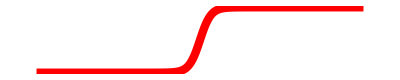

D:\Files\Research\Thesis\Proposal\arrow.png

```mathematica
arrow=Table[{x,(100/2)Tanh[2(0.5)x/100]},{x,-1500,1500,10}];
arr=Graphics[{Red,Thickness[0.015],Arrowheads[0.075],Arrow[arrow]}]
Export[NotebookDirectory[]<>"arrow.png",arr,Background->None]
```

## Mallinckrodt comparison

```mathematica
x1=Import["D:\\Files\\Research\\ARCS\\OSSE7_1b\\simgrid.h5","/x1"][[3;;-3]]/1000;
x3=Import["D:\\Files\\Research\\ARCS\\OSSE7_1b\\simgrid.h5","/x3"][[3;;-3]]/1000;
J1=Import["D:\\Files\\Research\\ARCS\\OSSE7_1b\\20150201_36000.000000.h5","/J1all"][[;;,55,;;]]/10^-6;
J3=Import["D:\\Files\\Research\\ARCS\\OSSE7_1b\\20150201_36000.000000.h5","/J3all"][[;;,55,;;]]/10^-6;
dat=Flatten[Table[{{x3[[j]],x1[[k]]},{J3[[j,k]],J1[[j,k]]}},{j,1,216},{k,1,100}],1];
dat1=Flatten[Table[{{x3[[j]],x1[[k]],J1[[j,k]]}},{j,1,216},{k,1,100}],2];
MinMax[J1]
```

{-41.2137,28.9655}

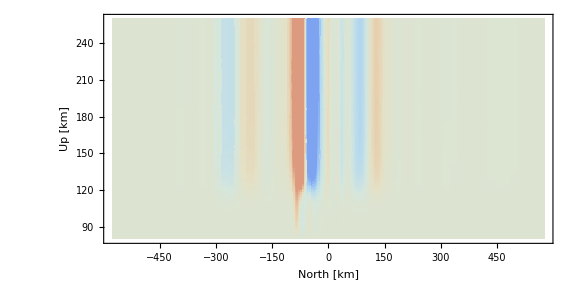

```mathematica
back=ListDensityPlot[dat1,FrameStyle->Directive[Black,14],FrameLabel->{"North [km]","Up [km]"},PlotRange->{All,{80,260}},InterpolationOrder->0,ColorFunctionScaling->False
,ColorFunction->(ColorData[{"ThermometerColors","Reverse"}][Rescale[#,{-30,30}]]&),PlotLegends->BarLegend[{Automatic,{-30,30}},LegendLabel->"j_(||) [mA/m^2]"],LabelStyle->Directive[Black,14],AspectRatio->1/2,ClippingStyle->Automatic,ImageSize->Large]
```

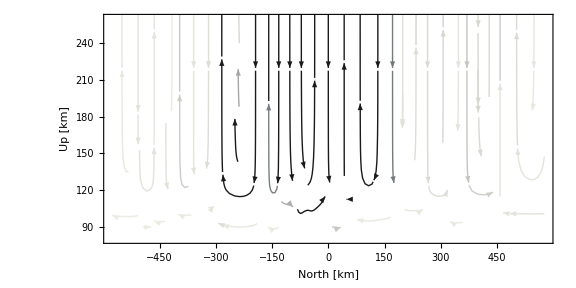

```mathematica
mallinckrodt=ListStreamPlot[dat[[;;;;1]],PlotRange->{All,{80,260}},Frame->True,FrameStyle->Directive[Black,14],FrameLabel->{"North [km]","Up [km]"},StreamColorFunction->ColorData[{"GrayTones","Reverse"}],StreamColorFunctionScaling->False,AspectRatio->1/2,ImageSize->Large]
```

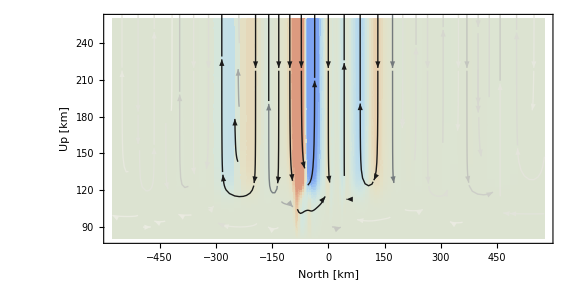

```mathematica
final=Show[back,mallinckrodt]
```

```mathematica
Export[NotebookDirectory[]<>"mallinckrodt_comp.png",final]
```

D:\Files\Research\Thesis\Proposal\mallinckrodt_comp.png

## Flow shear vs FAC

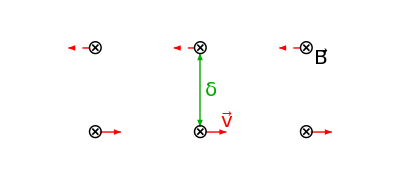

```mathematica
ff0=Graphics[{
{Black,Table[Text[Style["⊗",20],{x,0.4}],{x,-1,1,1}]}
,{Black,Table[Text[Style["⊗",20],{x,-0.4}],{x,-1,1,1}]}
,{Black,Text[Style["B⃗",20],{1.15,0.3}]}
,{Red,Dashed,Table[Arrow[{{x-0.05,0.4},{x-0.25,0.4}}],{x,-1,1,1}]}
,{Red,Text[Style["v⃗",20],{0.25,-0.3}]}
,{Red,Table[Arrow[{{x+0.05,-0.4},{x+0.25,-0.4}}],{x,-1,1,1}]}
,{Darker@Green,Arrowheads[{-.04,.04}],Arrow[{{0,-0.35},{0,0.35}}]}
,{Darker@Green,Text[Style["δ",20],{0.1,0}]}
},PlotRange->{{-1.55,1.55},{-0.7,0.7}}]
```

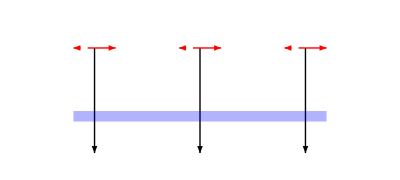

```mathematica
ff1=Graphics[{
{Black,Table[Arrow[{{x,1},{x,0}}],{x,-1,1,1}]}
,{Red,Table[Arrow[{{x,1},{x+0.2,1}}],{x,-1,1,1}]}
,{Red,Dashed,Table[Arrow[{{x,1},{x-0.2,1}}],{x,-1,1,1}]}
,{Blue,Opacity[0.3],Rectangle[{-1.2,0.3},{1.2,0.4}]}
},PlotRange->{{-1.55,1.55},{-0.1,1.3}}]
```

```mathematica
ff2=Graphics[{
{Black,Table[Arrow[BSplineCurve[{{x+0.1,1},{x,0.5},{x,0}}]],{x,-1,1,1}]}
,{Dashed,Table[Arrow[BSplineCurve[{{x-0.1,1},{x,0.5},{x,0}}]],{x,-1,1,1}]}
,{Red,Table[Arrow[{{x+0.1,1},{x+0.3,1}}],{x,-1,1,1}]}
,{Red,Dashed,Table[Arrow[{{x-0.1,1},{x-0.3,1}}],{x,-1,1,1}]}
,{Blue,Opacity[0.3],Rectangle[{-1.2,0.3},{1.2,0.4}]}
},PlotRange->{{-1.55,1.55},{-0.1,1.3}}]
```

-Graphics-

```mathematica
ff3=Graphics[{
{Black,Table[Arrow[BSplineCurve[{{x+0.2,1},{x,0.5},{x,0}}]],{x,-1,1,1}]}
,{Dashed,Table[Arrow[BSplineCurve[{{x-0.2,1},{x,0.5},{x,0}}]],{x,-1,1,1}]}
,{Red,Table[Arrow[{{x+0.2,1},{x+0.4,1}}],{x,-1,1,1}]}
,{Red,Dashed,Table[Arrow[{{x-0.2,1},{x-0.4,1}}],{x,-1,1,1}]}
,{Blue,Opacity[0.3],Rectangle[{-1.2,0.3},{1.2,0.4}]}
},PlotRange->{{-1.55,1.55},{-0.1,1.3}}]
```

-Graphics-

```mathematica
ff4=Graphics[{
{Black,Table[BSplineCurve[{{x+0.3,1},{x+0.1,0.4}}],{x,-1,1,1}]}
,{Dashed,Table[BSplineCurve[{{x-0.3,1},{x-0.1,0.4}}],{x,-1,1,1}]}
,{Black,Table[Arrow[{{x,0.3},{x,0}}],{x,-1,1,1}]}
,{Red,Table[Arrow[{{x+0.3,1},{x+0.5,1}}],{x,-1,1,1}]}
,{Red,Dashed,Table[Arrow[{{x-0.3,1},{x-0.5,1}}],{x,-1,1,1}]}
,{Blue,Opacity[0.3],Rectangle[{-1.2,0.3},{1.2,0.4}]}
},PlotRange->{{-1.55,1.55},{-0.1,1.3}}]
```

-Graphics-

```mathematica
ff5=Graphics[{
{Black,Table[Arrow[BSplineCurve[{{x+0.1,1},{x,0.5},{x,0}}]],{x,0,1,1}]}
,{Dashed,Table[Arrow[BSplineCurve[{{x-0.1,1},{x,0.5},{x,0}}]],{x,-1,0,1}]}
,{Red,Table[Arrow[{{x+0.1,1},{x+0.3,1}}],{x,0,2,1}]}
,{Red,Dashed,Table[Arrow[{{x-0.1,1},{x-0.3,1}}],{x,-2,0,1}]}
,{Blue,Opacity[0.3],Rectangle[{-1.2,0.3},{1.2,0.4}]}
,{Darker@Green,BSplineCurve[{{-0.09,0.95},{0,1},{0.09,0.95}}]}
,Text[Style["2α",20,Darker@Green],{0,1.1}]
},PlotRange->{{-1.55,1.55},{-0.1,1.3}}]
```

-Graphics-

```mathematica
GraphicsGrid[{{ff0,ff1,ff2},{ff3,ff4,ff5}},Frame->All]
```

-Graphics-